HW3 - Machine Learning on Dataset 2

Completed By: Deepak Singh

Importing the dataset

```mathematica
tornados=ResourceObject["Tornadoes in the U.S., 1950-2015"];
dataset=ResourceData[tornados,"Dataset"]
```

Dataset[<>]
 |  |  |  |

```mathematica
mag = dataset[[All,5]];
newscale={};
len = Length[mag];
For[i = 1,i ≤ len  ,i = i+1,AppendTo[newscale,StringTake[mag[i],-2]]]
mapped=dataset[MapThread[Append,{#,"newscale"->newscale//Thread}]&]
```

Dataset[<>]
 |  |  |  |

Removing the entries that have MagnitudeestimatedQ as False.

```mathematica
withoutEF=mapped[Select[#MagnitudeEstimatedQ&]];
```

Removing entries that don’t have start coordinates.

```mathematica
withoutMissingstart=withoutEF[Select[Not[MissingQ[#Start]]&]];
```

Replacing distances of data rows that don’t have end coordinates with zero and remaining one’s with the GeoDistance between the coordinates.

```mathematica
start=withoutMissingstart[[All,10]];
end=withoutMissingstart[[All,11]];
length = Length[start];
list = {}
For[i = 1, i ≤ length,i = i+1 ,If[end[[i]]== Missing["NotAvailable"],AppendTo[list,i]]];
```

{}
 |  |  |  |

```mathematica
d = {}
For[i = 1, i ≤ length, i= i+1,
	If[MemberQ[list,i],AppendTo[d,0],AppendTo[d,QuantityMagnitude[Quantity[GeoDistance[start[i],end[i]],"Miles"]]]]]
```

{}
 |  |  |  |

Appending the new distances to the dataset.

```mathematica
withdistance=withoutMissingstart[MapThread[Append,{#,"dist"->d//Thread}]&];
```

Replacing the range of the property loss with the average of the Property Loss.

```mathematica
withinterval = withdistance/.Interval[{min__,max__}]->Mean[{min,max}];
```

Replacing the rows with no property loss with the average property loss of the particular class of tornado.

```mathematica
listinterval={};
interval=withinterval[[All,8]];
For[i = 1, i ≤ length,i = i+1 ,If[interval[[i]]== Missing["NotAvailable"],AppendTo[listinterval,i]]]
```

```mathematica
propertyloss = {}
For[i = 1, i ≤ length, i= i+1,
	If[MemberQ[listinterval,i],AppendTo[propertyloss,25],AppendTo[propertyloss,QuantityMagnitude[Quantity[interval[i],"USDollars"]]]]]
```

{}
 |  |  |  |

Mapping the property loss, distance, injuries to the magnitude of the tornado.

```mathematica
withpropertyloss=withinterval[MapThread[Append,{#,"propertyloss"->propertyloss//Thread}]&];
```

```mathematica
examples=Map[{#propertyloss, #dist,#Injuries}->#Magnitude&,Normal[withpropertyloss]];
```

Separating training and testing data.

```mathematica
training=Drop[examples,{1,-1,5}];
```

Random Forest Classification Algorithm

```mathematica
classifier=Classify[training,Method ->"RandomForest"];
testing=Take[examples,{1,-1,5}];
testResults=Map[classifier[Keys[#]]==Values[#]&,testing];
```

The classify functions generates 5 classes owing to the mapping of the EF scale to F scale.

Performance Measure calculation.
Accuracy

```mathematica
ClassifierMeasurements[classifier,testing,"Accuracy"]
```

0.983914
 |  |  |  |

Precision

```mathematica
ClassifierMeasurements[classifier,testing,"Precision"]
```

<|F0→1.,F1→0.962963,F2→1.,F3→1.,F4→Indeterminate|>
 |  |  |  |

Recall

```mathematica
ClassifierMeasurements[classifier,testing,"Recall"]
```

<|F0→0.980296,F1→1.,F2→1.,F3→0.818182,F4→Indeterminate|>
 |  |  |  |

ROC Curve

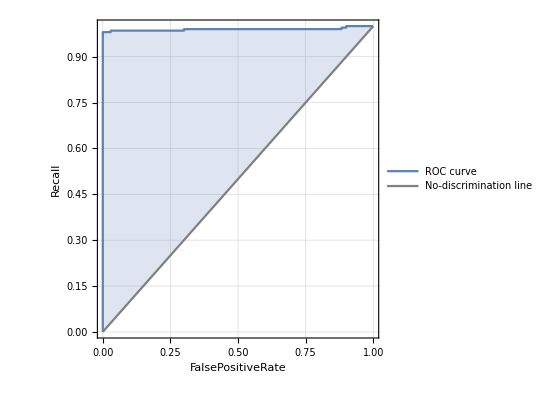
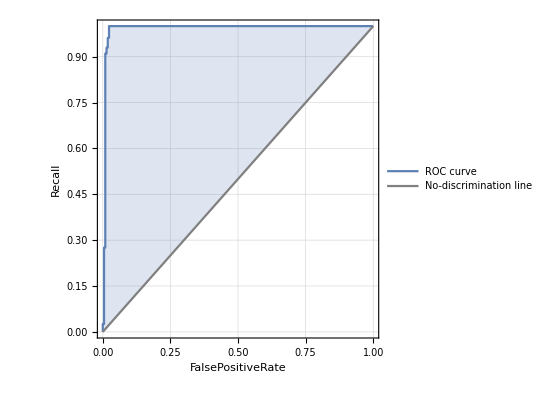
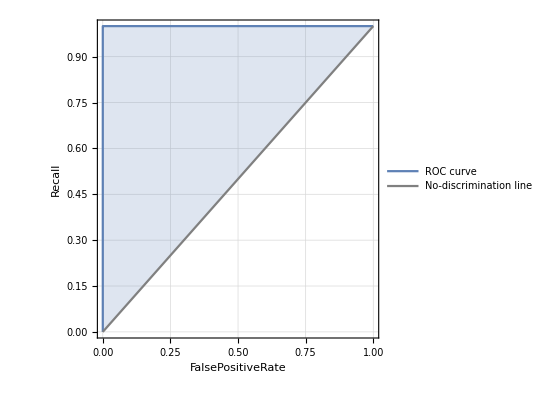
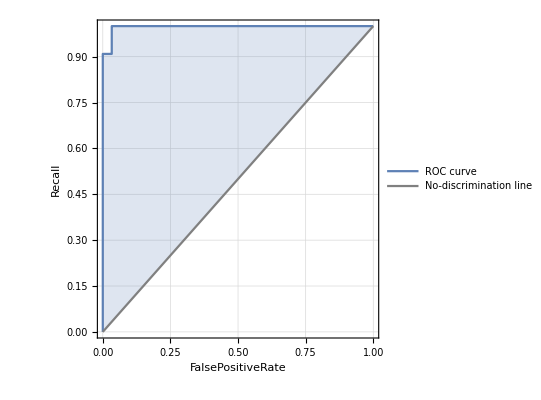
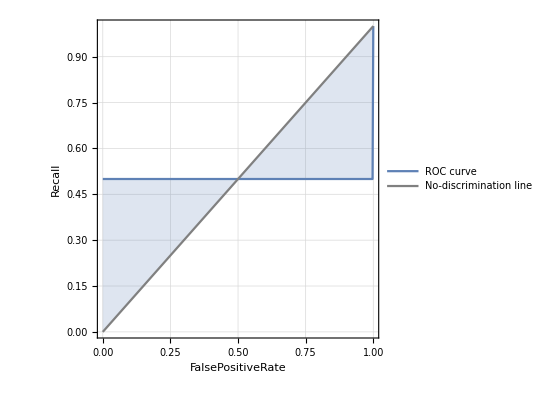
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-|>
 |  |  |  |

```mathematica
ClassifierMeasurements[classifier,testing,"ROCCurve"]
```

Neural Networks Algorithm

```mathematica
classifier=Classify[training,Method ->"NeuralNetwork"];
testing=Take[examples,{1,-1,5}];
testResults=Map[classifier[Keys[#]]==Values[#]&,testing];
```

Performance Measure calculation.
Accuracy

```mathematica
ClassifierMeasurements[classifier,testing,"Accuracy"]
```

0.640751
 |  |  |  |

Precision

```mathematica
ClassifierMeasurements[classifier,testing,"Precision"]
```

<|F0→0.621451,F1→0.804878,F2→Indeterminate,F3→0.6,F4→Indeterminate|>
 |  |  |  |

Recall

```mathematica
ClassifierMeasurements[classifier,testing,"Recall"]
```

<|F0→0.970443,F1→0.211538,F2→0.,F3→0.818182,F4→Indeterminate|>
 |  |  |  |

ROC Curve

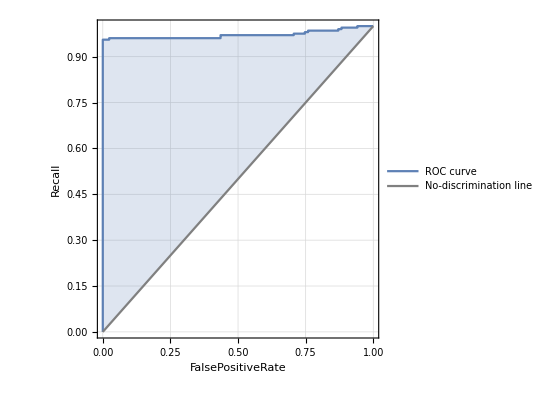
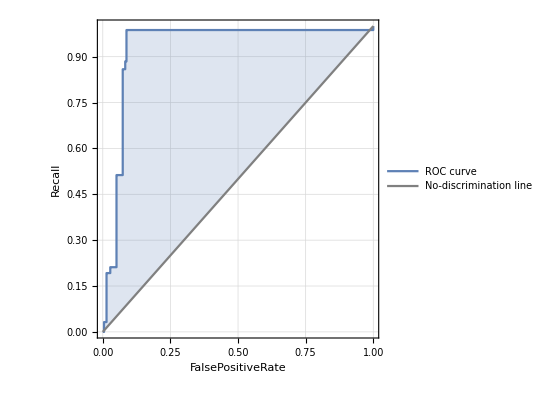
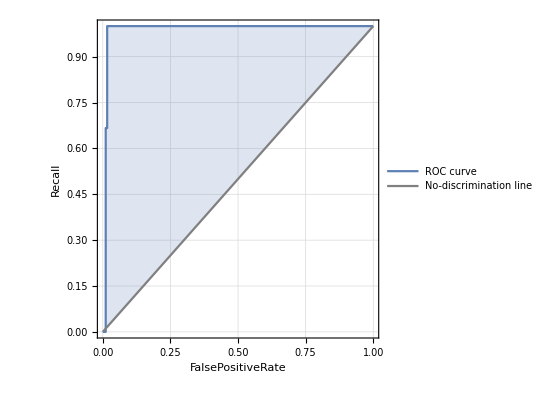
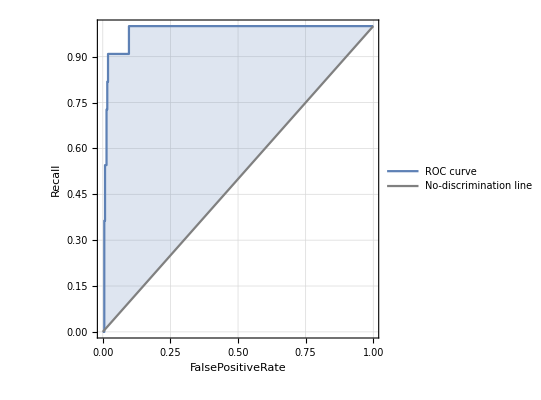
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-|>
 |  |  |  |

```mathematica
ClassifierMeasurements[classifier,testing,"ROCCurve"]
```

Nearest Neighbors Algorithm

```mathematica
classifier=Classify[training,Method ->"NearestNeighbors"];
testing=Take[examples,{1,-1,5}];
testResults=Map[classifier[Keys[#]]==Values[#]&,testing];
```

Performance Measure calculation.

Accuracy

```mathematica
ClassifierMeasurements[classifier,testing,"Accuracy"]
```

0.957105
 |  |  |  |

Precision

```mathematica
ClassifierMeasurements[classifier,testing,"Precision"]
```

<|F0→1.,F1→0.933333,F2→Indeterminate,F3→0.615385,F4→Indeterminate|>
 |  |  |  |

Recall

```mathematica
ClassifierMeasurements[classifier,testing,"Recall"]
```

<|F0→0.960591,F1→0.987179,F2→0.,F3→0.727273,F4→Indeterminate|>
 |  |  |  |

ROC Curve

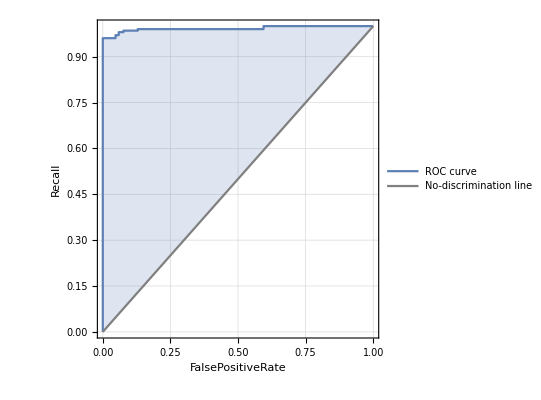
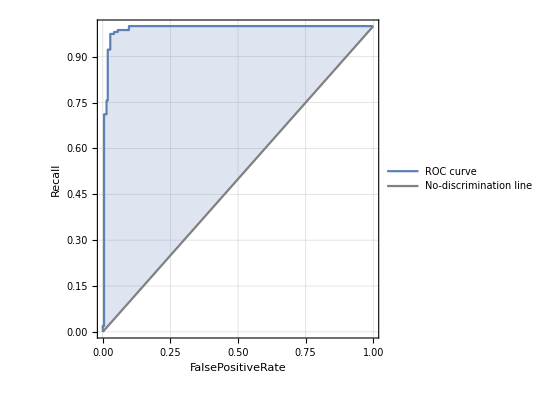
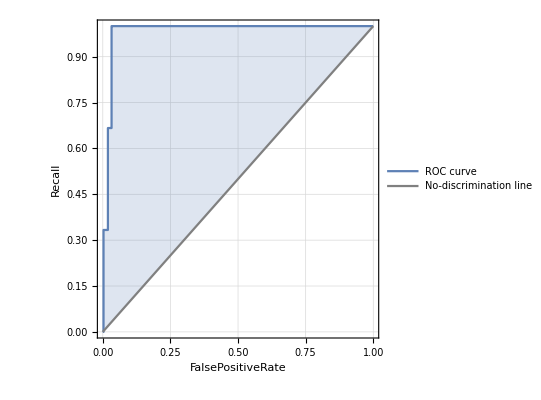
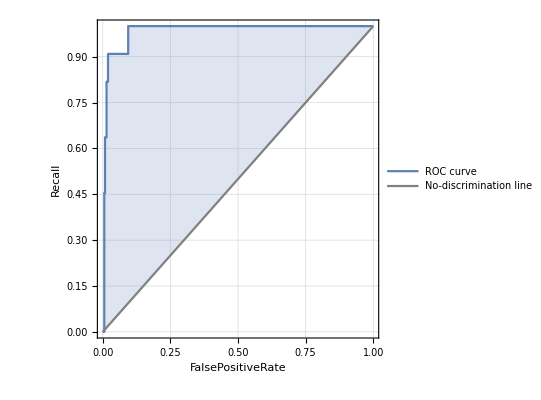
<|F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-|>
 |  |  |  |

```mathematica
ClassifierMeasurements[classifier,testing,"ROCCurve"]
```